```mathematica
dof[m_,n_]:=Simplify[(n(n-1)/2)-((n-m)(n-m-1)/2)]
```

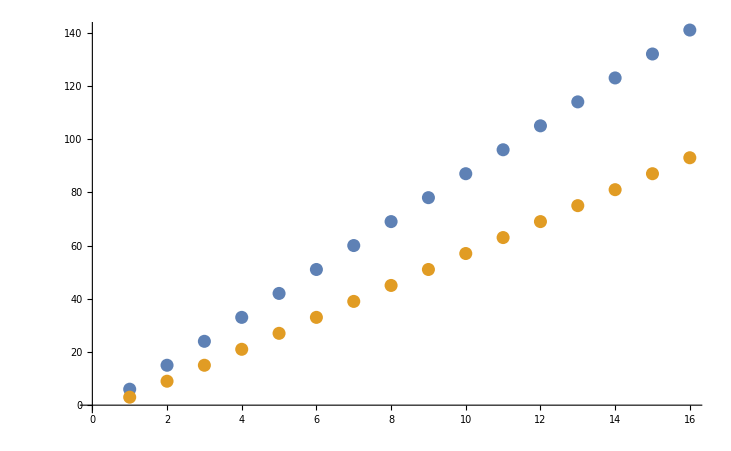

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[dof[m,n],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
rot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[tt],"=",ToString[t],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Cos[tt];mm[[i,j]]=-Sin[tt];mm[[j,i]]=Sin[tt];mm[[j,j]]=Cos[tt];mm)]
```

```mathematica
rot[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[x[2,3]] | -Sin[x[2,3]] | 0
0 | Sin[x[2,3]] | Cos[x[2,3]] | 0
0 | 0 | 0 | 1)

```mathematica
rot2[x_,i_,j_,n_]:=Module[{mm,xx},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[xx],"=",ToString[x],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Sqrt[1-xx];mm[[i,j]]=-Sqrt[xx];mm[[j,i]]=Sqrt[xx];mm[[j,j]]=Sqrt[1-xx];mm)]
```

```mathematica
rot2[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | √(1-x[2,3]) | -√x[2,3] | 0
0 | √x[2,3] | √(1-x[2,3]) | 0
0 | 0 | 0 | 1)

```mathematica
fullRotMat[t_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot[t,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat[t,1,3]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | Cos[t[1,3]])

```mathematica
fullRotMat2[x_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot2[x,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat2[t,1,3]//MatrixForm
```

(√(1-t[1,2]) √(1-t[1,3]) | -√t[1,2] | -√(1-t[1,2]) √t[1,3]
√t[1,2] √(1-t[1,3]) | √(1-t[1,2]) | -√t[1,2] √t[1,3]
√t[1,3] | 0 | √(1-t[1,3]))

```mathematica
sumRows[mm_,m_,n_]:=Table[Sum[Map[Abs,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
makeEqn[ms_,n_]:=Table[o==ms[[i]],{i,1,n}]
```

```mathematica
trySolve[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRows[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
sumRowsNoAbs[mm_,m_,n_]:=Table[Sum[mm[[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
trySolveNoAbs[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRowsNoAbs[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
makeSub[t_,x_,m_,n_]:=Flatten[Table[Table[{Sin[t[i,j]]->Sqrt[x[i,j]],Cos[t[i,j]]->Sqrt[1-x[i,j]]},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x_,m_,n_,xmin_,xmax_]:=Flatten[Table[Table[{xmin<=x[i,j]<=xmax},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x,2,3,0,1]
```

{0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[2,3]≤1}

```mathematica
makeCon[t,2,3,0,2Pi]
```

{0≤t[1,2]≤2 π,0≤t[1,3]≤2 π,0≤t[2,3]≤2 π}

```mathematica
mm=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mmzero=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm2=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm[[3,4]]=fullRotMat[t,3,4];mm2[[3,4]]=fullRotMat2[x,3,4];mm[[3,4]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]] | Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]] | Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]])-(-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]) Sin[t[3,4]]
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]] | Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]] | Cos[t[3,4]] (-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]])-(-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]]) Sin[t[3,4]]
Cos[t[1,4]] Sin[t[1,3]] | Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]] | Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]] | Cos[t[3,4]] (-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[2,3]] Sin[t[3,4]]
Sin[t[1,4]] | Cos[t[1,4]] Sin[t[2,4]] | Cos[t[1,4]] Cos[t[2,4]] Sin[t[3,4]] | Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,4]])

```mathematica
mmzero[[3,4]]=mm[[3,4]][[;;,1;;3]]/.{t[1,4]->0,t[1,3]->0,t[2,4]->0};mmzero[[3,4]]//MatrixForm
```

(Cos[t[1,2]] | -Cos[t[2,3]] Sin[t[1,2]] | Cos[t[3,4]] Sin[t[1,2]] Sin[t[2,3]]
Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]] | -Cos[t[1,2]] Cos[t[3,4]] Sin[t[2,3]]
0 | Sin[t[2,3]] | Cos[t[2,3]] Cos[t[3,4]]
0 | 0 | Sin[t[3,4]])

```mathematica
FullSimplify[Solve[Join[{mmzero[[3,4]][[1,1]]==mmzero[[3,4]][[2,1]]},makeCon[t,3,4,0,2Pi]],Reals],Assumptions->Join[{Reals},makeCon[t,3,4,0,2Pi]]]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

General::stop: Further output of Solve::fulldim will be suppressed during this calculation.

{{t[1,2]→π/4},{t[1,2]→(5 π)/4}}

```mathematica
mmzero00300401=mmzero[[3,4]]/.{t[1,2]->Pi/4,t[3,4]->ArcSin[p]};mmzero00300401//MatrixForm
```

(1/(√2) | -Cos[t[2,3]]/(√2) | (√(1-p^2) Sin[t[2,3]])/(√2)
1/(√2) | Cos[t[2,3]]/(√2) | -(√(1-p^2) Sin[t[2,3]])/(√2)
0 | Sin[t[2,3]] | √(1-p^2) Cos[t[2,3]]
0 | 0 | p)

```mathematica
FullSimplify[Solve[Join[{mmzero00300401[[3,1]]+mmzero00300401[[3,2]]+mmzero00300401[[3,3]]==p},makeCon[t,3,4,0,2Pi]],{t[2,3]},Reals],Assumptions->Join[{Reals},makeCon[t,3,4,0,2Pi]]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{√(1-p^2) Cos[t[2,3]]+Sin[t[2,3]]==p,0≤t[1,2]≤2 π,0≤t[1,3]≤2 π,0≤t[1,4]≤2 π,0≤t[2,3]≤2 π,0≤t[2,4]≤2 π,0≤t[3,4]≤2 π},{t[2,3]},ℝ]

```mathematica
mmzero00300402=FullSimplify[mmzero00300401/.{t[2,3]->Root"1.28"Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880472861290292722`27.,1.44923165893723569767249898432495682581`27.}},1]1.2790386643494873,t[3,4]->Root"1.45"Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880472861290292722`27.,1.44923165893723569767249898432495682581`27.}},2]1.4492316589372356}];mmzero00300402//MatrixForm
```

(1/(√2) | -Cos[Root1.28Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},1]1.2790386643494873]/(√2) | (Cos[Root1.45Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},2]1.4492316589372356] Sin[Root1.28Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},1]1.2790386643494873])/(√2)
1/(√2) | Cos[Root1.28Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},1]1.2790386643494873]/(√2) | -(Cos[Root1.45Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},2]1.4492316589372356] Sin[Root1.28Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},1]1.2790386643494873])/(√2)
0 | Sin[Root1.28Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},1]1.2790386643494873] | Cos[Root1.28Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},1]1.2790386643494873] Cos[Root1.45Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},2]1.4492316589372356]
0 | 0 | Sin[Root1.45Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},2]1.4492316589372356])

```mathematica
N[mmzero00300402,10]//MatrixForm
```

(0.7071067812 | -0.2033894027 | 0.08212392687
0.7071067812 | 0.2033894027 | -0.08212392687
0 | 0.9577397881 | 0.0348803227
0 | 0 | 0.9926201108)

```mathematica
FullSimplify[Sin[Root"1.45"Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880472861290292722`27.,1.44923165893723569767249898432495682581`27.}},2]1.4492316589372356]]
```

Sin[Root1.45Root[{{√2+√2 Cos[#1]-2 Cos[#1] Cos[#2]-2 Sin[#1]+√2 Cos[#2] Sin[#1]&,√2+√2 Cos[#1]+√2 Cos[#2] Sin[#1]-2 Sin[#2]&},{1.27903866434948724288880473,1.44923165893723569767249898}},2]1.4492316589372356]

```mathematica
eqn01=FullSimplify[mmzero00300401[[1,1]]-mmzero00300401[[1,2]]+mmzero00300401[[1,3]]==mmzero00300401[[3,1]]+mmzero00300401[[3,2]]+mmzero00300401[[3,3]],Assumptions->Join[{Reals},makeCon[t,3,4,0,2Pi]]]
```

(1+Cos[t[2,3]]+Cos[t[3,4]] Sin[t[2,3]])/(√2)==Cos[t[2,3]] Cos[t[3,4]]+Sin[t[2,3]]

```mathematica
eqn02=FullSimplify[mmzero00300401[[1,1]]-mmzero00300401[[1,2]]+mmzero00300401[[1,3]]==mmzero00300401[[4,1]]+mmzero00300401[[4,2]]+mmzero00300401[[4,3]],Assumptions->Join[{Reals},makeCon[t,3,4,0,2Pi]]]
```

(1+Cos[t[2,3]]+Cos[t[3,4]] Sin[t[2,3]])/(√2)==Sin[t[3,4]]

```mathematica
mmzero00300402=mmzero00300401/.{t[1,2]->Pi/4};mmzero00300402//MatrixForm
```

(1/(√2) | -Cos[t[2,3]]/(√2) | (Cos[t[3,4]] Sin[t[2,3]])/(√2)
1/(√2) | Cos[t[2,3]]/(√2) | -(Cos[t[3,4]] Sin[t[2,3]])/(√2)
0 | Sin[t[2,3]] | Cos[t[2,3]] Cos[t[3,4]]
0 | 0 | Sin[t[3,4]])

```mathematica
mmzero00300402/.{o->0.992620,t[2,3]->ArcSin[0.957740]}//MatrixForm
```

(1/(√2) | -0.203389 | 0.677224 Cos[t[3,4]]
1/(√2) | 0.203389 | -0.677224 Cos[t[3,4]]
0 | 0.95774 | 0.287635 Cos[t[3,4]]
0 | 0 | Sin[t[3,4]])

```mathematica
Solve[{mmzero00300402[[3,2]]+mmzero00300402[[3,3]]==o,0<o<1,0<=t[2,3]<2Pi},t[2,3],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Cos[t[2,3]] Cos[t[3,4]]+Sin[t[2,3]]==o,0<o<1,0≤t[2,3]<2 π},t[2,3],ℝ]

```mathematica
Solve[{mmzero00300402[[2,1]]+mmzero00300402[[2,2]]-mmzero00300402[[2,3]]==o,0<o<1,0<=t[2,3]<2Pi},t[2,3],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{1/(√2)+Cos[t[2,3]]/(√2)+(Cos[t[3,4]] Sin[t[2,3]])/(√2)==o,0<o<1,0≤t[2,3]<2 π},t[2,3],ℝ]

```mathematica
eqn01=mmzero00300402[[2,1]]+mmzero00300402[[2,2]]-mmzero00300402[[2,3]]==o
```

1/(√2)+Cos[t[2,3]]/(√2)+(Cos[t[3,4]] Sin[t[2,3]])/(√2)==o

```mathematica
eqn02=mmzero00300402[[3,2]]+mmzero00300402[[3,3]]==o
```

Cos[t[2,3]] Cos[t[3,4]]+Sin[t[2,3]]==o

```mathematica
eqn01=Expand[DivideSides[eqn01,(√(1-o^2))/(√2),Assumptions->(√(1-o^2))/(√2)!=0]]
```

1/(√(1-o^2))+Cos[t[2,3]]/(√(1-o^2))+(Cos[t[3,4]] Sin[t[2,3]])/(√(1-o^2))==(√2 o)/(√(1-o^2))

```mathematica
eqn03=FullSimplify[Inner[Subtract,eqn01,eqn02,Equal],Assumptions->{Reals,0<o<1}]
```

√2 o+Cos[t[2,3]] (-1+√(1-o^2) Cos[t[3,4]])+(√(1-o^2)-Cos[t[3,4]]) Sin[t[2,3]]==1+o √(1-o^2)

```mathematica
FullSimplify[Solve[{eqn03,0<o<1,0<=t[2,3]<2Pi},t[2,3],Reals]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{√2 o+Cos[t[2,3]] (-1+√(1-o^2) Cos[t[3,4]])+(√(1-o^2)-Cos[t[3,4]]) Sin[t[2,3]]==1+o √(1-o^2),0<o<1,0≤t[2,3]<2 π},t[2,3],ℝ]

```mathematica
mmzero00300403=FullSimplify[mmzero00300402/.{t[2,3]->ArcCos[(-1+√2 o-o √(1-o^2))/o^2]},Assumptions->{Reals,1/Sqrt[2]<o<1}];mmzero00300403//MatrixForm
```

(1/(√2) | (√2+o (-2+√(2-2 o^2)))/(2 o^2) | (√(1-((1+o (-√2+√(1-o^2)))^2)/o^4) Cos[t[3,4]])/(√2)
1/(√2) | -(√2+o (-2+√(2-2 o^2)))/(2 o^2) | -(√(1-((1+o (-√2+√(1-o^2)))^2)/o^4) Cos[t[3,4]])/(√2)
0 | √(1-((1+o (-√2+√(1-o^2)))^2)/o^4) | ((-1+o (√2-√(1-o^2))) Cos[t[3,4]])/o^2
0 | 0 | Sin[t[3,4]])

```mathematica
N[mmzero00300403/.{o->0.992620}]//MatrixForm
```

(0.707107 | -0.203389 | 0.677225 Cos[t[3.,4.]]
0.707107 | 0.203389 | -0.677225 Cos[t[3.,4.]]
0. | 0.95774 | 0.287635 Cos[t[3.,4.]]
0. | 0. | Sin[t[3.,4.]])

```mathematica
Solve[{mmzero00300403[[3,2]]+mmzero00300403[[3,3]]==o},o,Reals]
```

{{o→ConditionalExpression[Root[1+2 Cos[t[3,4]]^2+Cos[t[3,4]]^4+(-4 √2-8 √2 Cos[t[3,4]]^2-4 √2 Cos[t[3,4]]^4) #1+(10+20 Cos[t[3,4]]^2+10 Cos[t[3,4]]^4) #1^2+(-4 √2+4 Cos[t[3,4]]-8 √2 Cos[t[3,4]]^2+4 Cos[t[3,4]]^3-4 √2 Cos[t[3,4]]^4) #1^3+(1-12 √2 Cos[t[3,4]]+4 Cos[t[3,4]]^2-12 √2 Cos[t[3,4]]^3+3 Cos[t[3,4]]^4) #1^4+(20 Cos[t[3,4]]-4 √2 Cos[t[3,4]]^2+20 Cos[t[3,4]]^3-4 √2 Cos[t[3,4]]^4) #1^5+(-2-4 √2 Cos[t[3,4]]+4 Cos[t[3,4]]^2-4 √2 Cos[t[3,4]]^3+2 Cos[t[3,4]]^4) #1^6+(-4 √2-12 √2 Cos[t[3,4]]^2+4 Cos[t[3,4]]^3) #1^7+(10+14 Cos[t[3,4]]^2-4 √2 Cos[t[3,4]]^3+Cos[t[3,4]]^4) #1^8+4 Cos[t[3,4]] #1^9+(-4-4 √2 Cos[t[3,4]]+2 Cos[t[3,4]]^2) #1^10+#1^12&,3], ]},{o→ConditionalExpression[Root[1+2 Cos[t[3,4]]^2+Cos[t[3,4]]^4+(-4 √2-8 √2 Cos[t[3,4]]^2-4 √2 Cos[t[3,4]]^4) #1+(10+20 Cos[t[3,4]]^2+10 Cos[t[3,4]]^4) #1^2+(-4 √2+4 Cos[t[3,4]]-8 √2 Cos[t[3,4]]^2+4 Cos[t[3,4]]^3-4 √2 Cos[t[3,4]]^4) #1^3+(1-12 √2 Cos[t[3,4]]+4 Cos[t[3,4]]^2-12 √2 Cos[t[3,4]]^3+3 Cos[t[3,4]]^4) #1^4+(20 Cos[t[3,4]]-4 √2 Cos[t[3,4]]^2+20 Cos[t[3,4]]^3-4 √2 Cos[t[3,4]]^4) #1^5+(-2-4 √2 Cos[t[3,4]]+4 Cos[t[3,4]]^2-4 √2 Cos[t[3,4]]^3+2 Cos[t[3,4]]^4) #1^6+(-4 √2-12 √2 Cos[t[3,4]]^2+4 Cos[t[3,4]]^3) #1^7+(10+14 Cos[t[3,4]]^2-4 √2 Cos[t[3,4]]^3+Cos[t[3,4]]^4) #1^8+4 Cos[t[3,4]] #1^9+(-4-4 √2 Cos[t[3,4]]+2 Cos[t[3,4]]^2) #1^10+#1^12&,4], ]}}

```mathematica
N[mmzero00300403/.{o->Root"0.886"Root[{-2+#1^2&,4-16 #1 #2+36 #2^2-39 #2^4+20 #1 #2^5-16 #1 #2^7+16 #2^8&},{2,3}]0.8858199410524726}]//MatrixForm
```

(0.707107 | 0.142658 | 0.692567 Cos[t[3.,4.]]
0.707107 | -0.142658 | -0.692567 Cos[t[3.,4.]]
0. | 0.979437 | -0.201749 Cos[t[3.,4.]]
0. | 0. | Sin[t[3.,4.]])

```mathematica
N[mmzero00300403/.{o->Root"0.993"Root[{-2+#1^2&,4-16 #1 #2+36 #2^2-39 #2^4+20 #1 #2^5-16 #1 #2^7+16 #2^8&},{2,4}]0.9926201107977721}]//MatrixForm
```

(0.707107 | -0.203389 | 0.677224 Cos[t[3.,4.]]
0.707107 | 0.203389 | -0.677224 Cos[t[3.,4.]]
0. | 0.95774 | 0.287636 Cos[t[3.,4.]]
0. | 0. | Sin[t[3.,4.]])

```mathematica
oo=o/.{o->Root"0.993"Root[{-2+#1^2&,4-16 #1 #2+36 #2^2-39 #2^4+20 #1 #2^5-16 #1 #2^7+16 #2^8&},{2,4}]0.9926201107977721};
FullSimplify[(oo)]
N[(oo),50]
FullSimplify[(oo^2)]
N[(oo^2),50]
FullSimplify[(1/oo)]
N[(1/oo),50]
FullSimplify[(1/oo^2)]
N[(1/oo^2),50]
```

Root0.993Root[{-2+#1^2&,4-16 #1 #2+36 #2^2-39 #2^4+20 #1 #2^5-16 #1 #2^7+16 #2^8&},{2,4}]0.9926201107977721

0.9926201107977721067637721292356853318742001076216

Root0.985Root[4-28 #1-7 #1^2+16 #1^3+16 #1^4&,2]0.9852946843601814

0.98529468436018137337801480420402781677297161450111

Root1.01Root[16+16 #1^2-7 #1^4-28 #1^6+4 #1^8&,3]1.0074347568842794

1.0074347568842793760982535952310991419256901141137

Root1.01Root[16+16 #1-7 #1^2-28 #1^3+4 #1^4&,1]1.0149247893784872

1.0149247893784870917727027004682468870865135994956

```mathematica
mm[[3,7]]=fullRotMat[t,3,7];mm2[[3,7]]=fullRotMat2[x,3,7];mm[[3,7]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] | Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]] | Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]] | Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]])-(-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]) Sin[t[3,4]] | Cos[t[3,5]] (-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]])-(Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]]) Sin[t[3,5]] | Cos[t[3,6]] (-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]])-(Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]]) Sin[t[3,6]] | Cos[t[3,7]] (-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]])-(Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]) Sin[t[3,7]]
Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,2]] | Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] Sin[t[1,7]] Sin[t[2,7]] | Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,2]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,2]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]] | Cos[t[3,4]] (-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]])-(-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]]) Sin[t[3,4]] | Cos[t[3,5]] (-Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]])-(Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]]) Sin[t[3,5]] | Cos[t[3,6]] (-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,2]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]])-(Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]]) Sin[t[3,6]] | Cos[t[3,7]] (-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,2]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]])-(Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,2]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]) Sin[t[3,7]]
Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,3]] | Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]] | Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,3]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,3]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]] | Cos[t[3,4]] (-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[2,3]] Sin[t[3,4]] | Cos[t[3,5]] (-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]])-(Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]]) Sin[t[3,5]] | Cos[t[3,6]] (-Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,3]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]])-(Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]]) Sin[t[3,6]] | Cos[t[3,7]] (-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,3]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]])-(Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,3]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]) Sin[t[3,7]]
Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] | Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]] | Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,4]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]] | Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,4]] | Cos[t[3,5]] (-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[2,4]] Sin[t[3,4]] Sin[t[3,5]] | Cos[t[3,6]] (-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]])-(Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]]) Sin[t[3,6]] | Cos[t[3,7]] (-Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,4]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]])-(Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]) Sin[t[3,7]]
Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] | Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]] | Cos[t[3,7]] (Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]+(-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,5]] Sin[t[1,7]]-(Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]] | 0 | Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,5]] | Cos[t[3,6]] (-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[2,5]] Sin[t[3,5]] Sin[t[3,6]] | Cos[t[3,7]] (-Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,5]] Sin[t[1,7]]-(Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]])-(Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]+(-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]]) Sin[t[3,6]]) Sin[t[3,7]]
Cos[t[1,7]] Sin[t[1,6]] | Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]] | Cos[t[1,6]] Cos[t[2,6]] Cos[t[3,7]] Sin[t[3,6]]+(-Cos[t[2,7]] Sin[t[1,6]] Sin[t[1,7]]-Cos[t[1,6]] Sin[t[2,6]] Sin[t[2,7]]) Sin[t[3,7]] | 0 | 0 | Cos[t[1,6]] Cos[t[2,6]] Cos[t[3,6]] | Cos[t[3,7]] (-Cos[t[2,7]] Sin[t[1,6]] Sin[t[1,7]]-Cos[t[1,6]] Sin[t[2,6]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[2,6]] Sin[t[3,6]] Sin[t[3,7]]
Sin[t[1,7]] | Cos[t[1,7]] Sin[t[2,7]] | Cos[t[1,7]] Cos[t[2,7]] Sin[t[3,7]] | 0 | 0 | 0 | Cos[t[1,7]] Cos[t[2,7]] Cos[t[3,7]])

```mathematica
mmzero[[3,7]]=mm[[3,7]][[;;,1;;3]]/.{t[1,7]->0,t[1,6]->0,t[1,5]->0,t[1,4]->0,t[2,7]->0,t[2,6]->0};mmzero[[3,7]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | Cos[t[2,4]] Cos[t[2,5]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) | Cos[t[3,6]] Cos[t[3,7]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]] Sin[t[3,4]])-Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,5]] Sin[t[3,5]])
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[2,4]] Cos[t[2,5]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) | Cos[t[3,6]] Cos[t[3,7]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]] Sin[t[3,4]])-Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,5]] Sin[t[3,5]])
Sin[t[1,3]] | Cos[t[1,3]] Cos[t[2,4]] Cos[t[2,5]] Sin[t[2,3]] | Cos[t[3,6]] Cos[t[3,7]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]] Sin[t[3,4]])-Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]] Sin[t[2,5]] Sin[t[3,5]])
0 | Cos[t[2,5]] Sin[t[2,4]] | Cos[t[3,6]] Cos[t[3,7]] (Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-Sin[t[2,4]] Sin[t[2,5]] Sin[t[3,5]])
0 | Sin[t[2,5]] | Cos[t[2,5]] Cos[t[3,6]] Cos[t[3,7]] Sin[t[3,5]]
0 | 0 | Cos[t[3,7]] Sin[t[3,6]]
0 | 0 | Sin[t[3,7]])

```mathematica
mmzero00300701=mmzero[[3,7]]/.{t[3,7]->ArcSin[o],t[2,5]->ArcSin[o]};mmzero00300701//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | √(1-o^2) Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) | √(1-o^2) Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]] Sin[t[3,4]])-o Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[3,5]])
Cos[t[1,3]] Sin[t[1,2]] | √(1-o^2) Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) | √(1-o^2) Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]] Sin[t[3,4]])-o Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[3,5]])
Sin[t[1,3]] | √(1-o^2) Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]] | √(1-o^2) Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]] Sin[t[3,4]])-o Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]] Sin[t[3,5]])
0 | √(1-o^2) Sin[t[2,4]] | √(1-o^2) Cos[t[3,6]] (Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-o Sin[t[2,4]] Sin[t[3,5]])
0 | o | (1-o^2) Cos[t[3,6]] Sin[t[3,5]]
0 | 0 | √(1-o^2) Sin[t[3,6]]
0 | 0 | o)

```mathematica
Solve[mmzero00300701[[4,2]]==o,t[2,4],Reals]
```

{{t[2,4]→ConditionalExpression[π-ArcSin[o/(√(1-o^2))]+2 π C[1], C[1]∈ℤ&&-1/(√2)≤o≤1/(√2)]},{t[2,4]→ConditionalExpression[ArcSin[o/(√(1-o^2))]+2 π C[1], C[1]∈ℤ&&-1/(√2)≤o≤1/(√2)]}}

```mathematica
mmzero00300702=mmzero00300701/.{t[3,6]->π-ArcSin[o/(√(1-o^2))],t[2,4]->π-ArcSin[o/(√(1-o^2))]};mmzero00300702//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -√(1-o^2) √(1-o^2/(1-o^2)) (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) | -√(1-o^2) √(1-o^2/(1-o^2)) (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])-(o (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[3,4]])/(√(1-o^2)))+o √(1-o^2/(1-o^2)) (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[3,5]])
Cos[t[1,3]] Sin[t[1,2]] | -√(1-o^2) √(1-o^2/(1-o^2)) (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) | -√(1-o^2) √(1-o^2/(1-o^2)) (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])-(o (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[3,4]])/(√(1-o^2)))+o √(1-o^2/(1-o^2)) (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[3,5]])
Sin[t[1,3]] | -√(1-o^2) √(1-o^2/(1-o^2)) Cos[t[1,3]] Sin[t[2,3]] | -√(1-o^2) √(1-o^2/(1-o^2)) (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]-(o Cos[t[1,3]] Sin[t[2,3]] Sin[t[3,4]])/(√(1-o^2)))+o √(1-o^2/(1-o^2)) Cos[t[1,3]] Sin[t[2,3]] Sin[t[3,5]])
0 | o | -√(1-o^2) √(1-o^2/(1-o^2)) (-√(1-o^2/(1-o^2)) Cos[t[3,5]] Sin[t[3,4]]-(o^2 Sin[t[3,5]])/(√(1-o^2)))
0 | o | -((1-o^2) √(1-o^2/(1-o^2)) Sin[t[3,5]])
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00300703=mmzero00300702/.{t[2,3]->0,t[3,5]->0,t[3,4]->0};mmzero00300703//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | √(1-o^2) √(1-o^2/(1-o^2)) Sin[t[1,2]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | -√(1-o^2) √(1-o^2/(1-o^2)) Cos[t[1,2]] | √(1-o^2) √(1-o^2/(1-o^2)) Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | -√(1-o^2) √(1-o^2/(1-o^2)) Cos[t[1,3]]
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00300704=FullSimplify[mmzero00300703];mmzero00300704//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | √(1-2 o^2) Sin[t[1,2]] | √(1-2 o^2) Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | -√(1-2 o^2) Cos[t[1,2]] | √(1-2 o^2) Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | -√(1-2 o^2) Cos[t[1,3]]
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00300705=mmzero00300704/.{t[1,2]->Pi/4};mmzero00300705//MatrixForm
```

(Cos[t[1,3]]/(√2) | (√(1-2 o^2))/(√2) | (√(1-2 o^2) Sin[t[1,3]])/(√2)
Cos[t[1,3]]/(√2) | -(√(1-2 o^2))/(√2) | (√(1-2 o^2) Sin[t[1,3]])/(√2)
Sin[t[1,3]] | 0 | -√(1-2 o^2) Cos[t[1,3]]
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00300705/.{o->0.701815,t[1,3]->ArcSin[0.604540]}//MatrixForm
```

(0.563263 | 0.0863464 | 0.0521999
0.563263 | -0.0863464 | 0.0521999
0.60454 | 0 | -0.0972716
0 | 0.701815 | 0
0 | 0.701815 | 0
0 | 0 | 0.701815
0 | 0 | 0.701815)

```mathematica
Solve[{mmzero00300705[[3,1]]-mmzero00300705[[3,3]]==o,0<=o<1/2||1/2<o<=1,0<=t[1,3]<2Pi},t[1,3],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{√(1-2 o^2) Cos[t[1,3]]+Sin[t[1,3]]==o,0≤o<1/2||1/2<o≤1,0≤t[1,3]<2 π},t[1,3],ℝ]

```mathematica
Solve[{mmzero00300705[[2,1]]-mmzero00300705[[2,2]]+mmzero00300705[[2,3]]==o,0<=o<1/2||1/2<o<=1,0<=t[1,3]<2Pi},t[1,3],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==o,0≤o<1/2||1/2<o≤1,0≤t[1,3]<2 π},t[1,3],ℝ]

```mathematica
Solve[{-(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==o,0≤o<1/2||1/2<o≤1,0≤t[1,3]<2 π},t[1,3],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{-(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==o,0≤o<1/2||1/2<o≤1,0≤t[1,3]<2 π},t[1,3],ℝ]

```mathematica
Solve[{mmzero00300705[[2,1]]-mmzero00300705[[2,2]]+mmzero00300705[[2,3]]==mmzero00300705[[3,1]]-mmzero00300705[[3,3]],0<=o<1/2||1/2<o<=1,0<=t[1,3]<2Pi},t[1,3],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==√(1-2 o^2) Cos[t[1,3]]+Sin[t[1,3]],0≤o<1/2||1/2<o≤1,0≤t[1,3]<2 π},t[1,3],ℝ]

```mathematica
Solve[{mmzero00300705[[2,1]]-mmzero00300705[[2,2]]+mmzero00300705[[2,3]]==o,mmzero00300705[[3,1]]-mmzero00300705[[3,3]]==o,0<=o<1/2||1/2<o<=1,0<=t[1,3]<2Pi},{t[1,3],o},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==o,√(1-2 o^2) Cos[t[1,3]]+Sin[t[1,3]]==o,0≤o<1/2||1/2<o≤1,0≤t[1,3]<2 π},{t[1,3],o},ℝ]

```mathematica
eqn01=(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==o
```

(√(1-2 o^2))/(√2)+Cos[t[1,3]]/(√2)+(√(1-2 o^2) Sin[t[1,3]])/(√2)==o

```mathematica
eqn02=√(1-2 o^2) Cos[t[1,3]]+Sin[t[1,3]]==o
```

√(1-2 o^2) Cos[t[1,3]]+Sin[t[1,3]]==o

```mathematica
eqn01=FullSimplify[MultiplySides[eqn01,√2/√(1-2 o^2),Assumptions->{√2/√(1-2 o^2)!=0,o!=1/Sqrt[2]}]]
```

1+Cos[t[1,3]]/(√(1-2 o^2))+Sin[t[1,3]]==(2 o)/(√(2-4 o^2))

```mathematica
eqn03=FullSimplify[Inner[Subtract,eqn01,eqn02,Equal]]
```

1+o+(2 o^2 Cos[t[1,3]])/(√(1-2 o^2))==(2 o)/(√(2-4 o^2))

```mathematica
FullSimplify[Solve[eqn03,t[1,3],Reals],Assumptions->{Reals,o!=1/Sqrt[2],0<o<1,0<=t[1,3]<2Pi}]
```

{{t[1,3]→ConditionalExpression[-ArcSec[-(2 √2 o^2)/(√(2-4 o^2)+o (-2+√(2-4 o^2)))]+2 π C[1], ]},{t[1,3]→ConditionalExpression[ArcSec[-(2 √2 o^2)/(√(2-4 o^2)+o (-2+√(2-4 o^2)))]+2 π C[1], ]}}

```mathematica
mmzero00300706=FullSimplify[mmzero00300705/.{t[1,3]->ArcSec[-(2 √2 o^2)/(√(2-4 o^2)+o (-2+√(2-4 o^2)))]},Assumptions->{Reals,o!=1/Sqrt[2],0<o<1}];mmzero00300706//MatrixForm
```

(-(√(2-4 o^2)+o (-2+√(2-4 o^2)))/(4 o^2) | √(1/2-o^2) | √(1/2-o^2) √(1-((√(2-4 o^2)+o (-2+√(2-4 o^2)))^2)/(8 o^4))
-(√(2-4 o^2)+o (-2+√(2-4 o^2)))/(4 o^2) | -√(1/2-o^2) | √(1/2-o^2) √(1-((√(2-4 o^2)+o (-2+√(2-4 o^2)))^2)/(8 o^4))
√(1-((√(2-4 o^2)+o (-2+√(2-4 o^2)))^2)/(8 o^4)) | 0 | (1-o (-1+2 o (1+o)+√(2-4 o^2)))/(2 o^2)
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o)

```mathematica
Solve[mmzero00300706[[3,1]]-mmzero00300706[[3,3]]==o,o,Reals]
```

{{o→Root0.525Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,3]0.5251979161178214},{o→Root0.702Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416}}

```mathematica
N[FullSimplify[mmzero00300706/.{o->Root"0.525"Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,3]0.5251979161178214}]]//MatrixForm
```

(-0.356968 | 0.473463 | 0.408703
-0.356968 | -0.473463 | 0.408703
0.86322 | 0. | 0.338022
0. | 0.525198 | 0.
0. | 0.525198 | 0.
0. | 0. | 0.525198
0. | 0. | 0.525198)

```mathematica
N[FullSimplify[mmzero00300706/.{o->Root"0.702"Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416}]]//MatrixForm
```

(0.563264 | 0.0863494 | 0.0522016
0.563264 | -0.0863494 | 0.0522016
0.60454 | 0. | -0.0972749
0. | 0.701815 | 0.
0. | 0.701815 | 0.
0. | 0. | 0.701815
0. | 0. | 0.701815)

```mathematica
oo=o/.{o->Root"0.702"Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416};
FullSimplify[(oo)]
N[(oo),50]
FullSimplify[(oo^2)]
N[(oo^2),50]
FullSimplify[(1/oo)]
N[(1/oo),50]
FullSimplify[(1/oo^2)]
N[(1/oo^2),50]
```

Root0.702Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416

0.70181463472204163273690096732053872531214164001701

(Root0.702Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416)^2

0.4925437815100327249453652607539894710515583740145

Root1.42Root[25-8 #1-8 #1^2+36 #1^3+2 #1^4-24 #1^5-4 #1^6+4 #1^7+#1^8&,3]1.4248776678703157

1.4248776678703154574582007518740132095227540004765

1/((Root0.702Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416)^2)

2.0302763683955490069116066701864568825638265619853

```mathematica
mm[[3,10]]=fullRotMat[t,3,10];mm2[[3,10]]=fullRotMat2[x,3,10];mm[[3,10]]//MatrixForm
```

```mathematica
mmzero[[3,10]]=mm[[3,10]][[;;,1;;3]]/.{t[1,10]->0,t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[1,5]->0,t[2,10]->0,t[2,9]->0,t[2,8]->0};mmzero[[3,10]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,6]] Sin[t[3,6]])-Cos[t[2,5]] Cos[t[2,6]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,7]] Sin[t[3,7]])
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) | Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,6]] Sin[t[3,6]])-Cos[t[2,5]] Cos[t[2,6]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,7]] Sin[t[3,7]])
Cos[t[1,4]] Sin[t[1,3]] | Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,6]] Sin[t[3,6]])-Cos[t[2,5]] Cos[t[2,6]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,7]] Sin[t[3,7]])
Sin[t[1,4]] | Cos[t[1,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Sin[t[2,4]] | Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]] Sin[t[3,5]])-Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]] Sin[t[2,6]] Sin[t[3,6]])-Cos[t[1,4]] Cos[t[2,5]] Cos[t[2,6]] Sin[t[2,4]] Sin[t[2,7]] Sin[t[3,7]])
0 | Cos[t[2,6]] Cos[t[2,7]] Sin[t[2,5]] | Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] (Cos[t[3,7]] (Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]-Sin[t[2,5]] Sin[t[2,6]] Sin[t[3,6]])-Cos[t[2,6]] Sin[t[2,5]] Sin[t[2,7]] Sin[t[3,7]])
0 | Cos[t[2,7]] Sin[t[2,6]] | Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] (Cos[t[2,6]] Cos[t[3,7]] Sin[t[3,6]]-Sin[t[2,6]] Sin[t[2,7]] Sin[t[3,7]])
0 | Sin[t[2,7]] | Cos[t[2,7]] Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] Sin[t[3,7]]
0 | 0 | Cos[t[3,9]] Cos[t[3,10]] Sin[t[3,8]]
0 | 0 | Cos[t[3,10]] Sin[t[3,9]]
0 | 0 | Sin[t[3,10]])

```mathematica
mmzero00301001=mmzero[[3,10]]/.{t[2,7]->ArcSin[o],t[3,10]->ArcSin[o]};mmzero00301001//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | √(1-o^2) Cos[t[2,5]] Cos[t[2,6]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) Cos[t[3,8]] Cos[t[3,9]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,6]] Sin[t[3,6]])-o Cos[t[2,5]] Cos[t[2,6]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | √(1-o^2) Cos[t[2,5]] Cos[t[2,6]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) Cos[t[3,8]] Cos[t[3,9]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,6]] Sin[t[3,6]])-o Cos[t[2,5]] Cos[t[2,6]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,4]] Sin[t[1,3]] | √(1-o^2) Cos[t[2,5]] Cos[t[2,6]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) Cos[t[3,8]] Cos[t[3,9]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,6]] Sin[t[3,6]])-o Cos[t[2,5]] Cos[t[2,6]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Sin[t[1,4]] | √(1-o^2) Cos[t[1,4]] Cos[t[2,5]] Cos[t[2,6]] Sin[t[2,4]] | √(1-o^2) Cos[t[3,8]] Cos[t[3,9]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]] Sin[t[3,5]])-Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]] Sin[t[2,6]] Sin[t[3,6]])-o Cos[t[1,4]] Cos[t[2,5]] Cos[t[2,6]] Sin[t[2,4]] Sin[t[3,7]])
0 | √(1-o^2) Cos[t[2,6]] Sin[t[2,5]] | √(1-o^2) Cos[t[3,8]] Cos[t[3,9]] (Cos[t[3,7]] (Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]-Sin[t[2,5]] Sin[t[2,6]] Sin[t[3,6]])-o Cos[t[2,6]] Sin[t[2,5]] Sin[t[3,7]])
0 | √(1-o^2) Sin[t[2,6]] | √(1-o^2) Cos[t[3,8]] Cos[t[3,9]] (Cos[t[2,6]] Cos[t[3,7]] Sin[t[3,6]]-o Sin[t[2,6]] Sin[t[3,7]])
0 | o | (1-o^2) Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,7]]
0 | 0 | √(1-o^2) Cos[t[3,9]] Sin[t[3,8]]
0 | 0 | √(1-o^2) Sin[t[3,9]]
0 | 0 | o)

```mathematica
mmzero00301002=mmzero00301001/.{t[2,6]->ArcSin[o/Sqrt[1-o^2]],t[3,9]->ArcSin[o/Sqrt[1-o^2]]};mmzero00301002//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-(o Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-o^2)) Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-(o Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-o^2)) Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,4]] Sin[t[1,3]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]] Sin[t[3,5]])-(o Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-o^2)) Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Sin[t[1,4]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]] Sin[t[3,5]])-(o Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]] Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-o^2)) Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]] Sin[t[3,7]])
0 | √(1-o^2) √(1-o^2/(1-o^2)) Sin[t[2,5]] | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]-(o Sin[t[2,5]] Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-o^2)) Sin[t[2,5]] Sin[t[3,7]])
0 | o | √(1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] (√(1-o^2/(1-o^2)) Cos[t[3,7]] Sin[t[3,6]]-(o^2 Sin[t[3,7]])/(√(1-o^2)))
0 | o | (1-o^2) √(1-o^2/(1-o^2)) Cos[t[3,8]] Sin[t[3,7]]
0 | 0 | √(1-o^2) √(1-o^2/(1-o^2)) Sin[t[3,8]]
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00301003=mmzero00301002/.{t[2,5]->ArcSin[o/Sqrt[1-2o^2]],t[3,8]->ArcSin[o/Sqrt[1-2o^2]]};mmzero00301003//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(o (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(o (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,4]] Sin[t[1,3]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])-(o (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Sin[t[1,4]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) Cos[t[1,4]] Sin[t[2,4]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-(o Cos[t[1,4]] Sin[t[2,4]] Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) Cos[t[1,4]] Sin[t[2,4]] Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) Cos[t[1,4]] Sin[t[2,4]] Sin[t[3,7]])
0 | (o √(1-o^2) √(1-o^2/(1-o^2)))/(√(1-2 o^2)) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (√(1-o^2/(1-2 o^2)) Cos[t[3,6]] Sin[t[3,5]]-(o^2 Sin[t[3,6]])/(√(1-2 o^2) √(1-o^2)))-(o^2 √(1-o^2/(1-o^2)) Sin[t[3,7]])/(√(1-2 o^2)))
0 | o | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (√(1-o^2/(1-o^2)) Cos[t[3,7]] Sin[t[3,6]]-(o^2 Sin[t[3,7]])/(√(1-o^2)))
0 | o | (1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) Sin[t[3,7]]
0 | 0 | (o √(1-o^2) √(1-o^2/(1-o^2)))/(√(1-2 o^2))
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00301004=ConstantArray[0,{10,3}];
Timing[mmzero00301004[[;;,1;;1]]=FullSimplify[mmzero00301003[[;;,1;;1]],Assumptions->Join[{Reals,0<=o<1/3||1/3<o<=1},makeCon[t,3,10,0,2Pi]]]][[1]]
Timing[mmzero00301004[[;;,2;;2]]=FullSimplify[mmzero00301003[[;;,2;;2]],Assumptions->Join[{Reals,0<=o<1/3||1/3<o<=1},makeCon[t,3,10,0,2Pi]]]][[1]]
Timing[mmzero00301004[[5;;10,3;;3]]=FullSimplify[mmzero00301003[[5;;10,3;;3]],Assumptions->Join[{Reals,0<=o<1/3||1/3<o<=1},makeCon[t,3,10,0,2Pi]]]][[1]]
mmzero00301004[[1;;4,3;;3]]=mmzero00301003[[1;;4,3;;3]];
mmzero00301004//MatrixForm
```

0.01662

0.688524

1.00669

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | -√(1-3 o^2) (Cos[t[2,3]] Cos[t[2,4]] Sin[t[1,2]]+Cos[t[1,2]] (Cos[t[2,4]] Sin[t[1,3]] Sin[t[2,3]]+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(o (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | √(1-3 o^2) (Cos[t[1,2]] Cos[t[2,3]] Cos[t[2,4]]-Sin[t[1,2]] (Cos[t[2,4]] Sin[t[1,3]] Sin[t[2,3]]+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])-(o (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Cos[t[1,4]] Sin[t[1,3]] | √(1-3 o^2) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])-(o (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[3,7]])
Sin[t[1,4]] | √(1-3 o^2) Cos[t[1,4]] Sin[t[2,4]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]-(o Cos[t[1,4]] Sin[t[2,4]] Sin[t[3,5]])/(√(1-2 o^2)))-(o √(1-o^2/(1-2 o^2)) Cos[t[1,4]] Sin[t[2,4]] Sin[t[3,6]])/(√(1-o^2)))-o √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) Cos[t[1,4]] Sin[t[2,4]] Sin[t[3,7]])
0 | o | √((1-3 o^2)/(1-3 o^2+2 o^4)) (√(1/2-(3 o^2)/2+o^4) √(3+1/(-1+2 o^2)) Cos[t[3,6]] Cos[t[3,7]] Sin[t[3,5]]-o^2 (Cos[t[3,7]] Sin[t[3,6]]+√(1-2 o^2) Sin[t[3,7]]))
0 | o | √((-1+3 o^2)/(-1+o^2)) (√(1-2 o^2) Cos[t[3,7]] Sin[t[3,6]]-o^2 Sin[t[3,7]])
0 | o | -((-1+o^2) √((-1+3 o^2)/(-1+o^2)) Sin[t[3,7]])
0 | 0 | o
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00301005=mmzero00301004/.{t[3,7]->0,t[3,6]->0,t[3,5]->0};mmzero00301005//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | -√(1-3 o^2) (Cos[t[2,3]] Cos[t[2,4]] Sin[t[1,2]]+Cos[t[1,2]] (Cos[t[2,4]] Sin[t[1,3]] Sin[t[2,3]]+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,4]] (-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | √(1-3 o^2) (Cos[t[1,2]] Cos[t[2,3]] Cos[t[2,4]]-Sin[t[1,2]] (Cos[t[2,4]] Sin[t[1,3]] Sin[t[2,3]]+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])
Cos[t[1,4]] Sin[t[1,3]] | √(1-3 o^2) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])
Sin[t[1,4]] | √(1-3 o^2) Cos[t[1,4]] Sin[t[2,4]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) Cos[t[1,4]] Cos[t[2,4]] Sin[t[3,4]]
0 | o | 0
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00301006=mmzero00301005/.{t[1,2]->Pi/4};mmzero00301006//MatrixForm
```

((Cos[t[1,3]] Cos[t[1,4]])/(√2) | -√(1-3 o^2) ((Cos[t[2,3]] Cos[t[2,4]])/(√2)+(Cos[t[2,4]] Sin[t[1,3]] Sin[t[2,3]]+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])/(√2)) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,4]] (-(Cos[t[2,3]] Sin[t[1,3]])/(√2)+Sin[t[2,3]]/(√2))+(-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]])/(√2)-(-Cos[t[2,3]]/(√2)-(Sin[t[1,3]] Sin[t[2,3]])/(√2)) Sin[t[2,4]]) Sin[t[3,4]])
(Cos[t[1,3]] Cos[t[1,4]])/(√2) | √(1-3 o^2) ((Cos[t[2,3]] Cos[t[2,4]])/(√2)-(Cos[t[2,4]] Sin[t[1,3]] Sin[t[2,3]]+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])/(√2)) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[3,4]] (-(Cos[t[2,3]] Sin[t[1,3]])/(√2)-Sin[t[2,3]]/(√2))+(-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]])/(√2)-(Cos[t[2,3]]/(√2)-(Sin[t[1,3]] Sin[t[2,3]])/(√2)) Sin[t[2,4]]) Sin[t[3,4]])
Cos[t[1,4]] Sin[t[1,3]] | √(1-3 o^2) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])
Sin[t[1,4]] | √(1-3 o^2) Cos[t[1,4]] Sin[t[2,4]] | √(1-o^2) √(1-o^2/(1-2 o^2)) √(1-o^2/(1-o^2)) Cos[t[1,4]] Cos[t[2,4]] Sin[t[3,4]]
0 | o | 0
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o
0 | 0 | o)

```mathematica
mmzero00301007=ConstantArray[0,{10,3}];
Timing[mmzero00301007[[;;,1;;1]]=FullSimplify[mmzero00301006[[;;,1;;1]],Assumptions->Join[{Reals,0<=o<1/3||1/3<o<=1},makeCon[t,3,10,0,2Pi]]]][[1]]
Timing[mmzero00301007[[;;,2;;2]]=FullSimplify[mmzero00301006[[;;,2;;2]],Assumptions->Join[{Reals,0<=o<1/3||1/3<o<=1},makeCon[t,3,10,0,2Pi]]]][[1]]
Timing[mmzero00301007[[;;,3;;3]]=FullSimplify[mmzero00301006[[;;,3;;3]],Assumptions->Join[{Reals,0<=o<1/3||1/3<o<=1},makeCon[t,3,10,0,2Pi]]]][[1]]
mmzero00301007//MatrixForm
```

0.012065

0.4614

2.61989

((Cos[t[1,3]] Cos[t[1,4]])/(√2) | -1/2 √(2-6 o^2) (Cos[t[2,4]] (Cos[t[2,3]]+Sin[t[1,3]] Sin[t[2,3]])+Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | (√(1-3 o^2) (Cos[t[3,4]] (-Cos[t[2,3]] Sin[t[1,3]]+Sin[t[2,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]+(Cos[t[2,3]]+Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]]))/(√2)
(Cos[t[1,3]] Cos[t[1,4]])/(√2) | 1/2 √(2-6 o^2) (Cos[t[2,4]] (Cos[t[2,3]]-Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | -(√(1-3 o^2) (Cos[t[3,4]] (Cos[t[2,3]] Sin[t[1,3]]+Sin[t[2,3]])+(Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]+(Cos[t[2,3]]-Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]]))/(√2)
Cos[t[1,4]] Sin[t[1,3]] | √(1-3 o^2) (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) | √(1-3 o^2) (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]]-(Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]+Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])
Sin[t[1,4]] | √(1-3 o^2) Cos[t[1,4]] Sin[t[2,4]] | √(1-3 o^2) Cos[t[1,4]] Cos[t[2,4]] Sin[t[3,4]]
0 | o | 0
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o
0 | 0 | o)

```mathematica
Solve[{mmzero00301007[[4,1]]==mmzero00301007[[2,1]],0<=o<1/3||1/3<o<=1,0<=t[1,4]<2Pi,0<=t[1,3]<2Pi},t[1,4],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Sin[t[1,4]]==(Cos[t[1,3]] Cos[t[1,4]])/(√2),0≤o<1/3||1/3<o≤1,0≤t[1,4]<2 π,0≤t[1,3]<2 π},t[1,4],ℝ]

```mathematica
Solve[{mmzero00301007[[4,1]]==mmzero00301007[[3,1]],0<=o<1/3||1/3<o<=1,0<=t[1,4]<2Pi,0<=t[1,3]<2Pi},t[1,4],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Sin[t[1,4]]==Cos[t[1,4]] Sin[t[1,3]],0≤o<1/3||1/3<o≤1,0≤t[1,4]<2 π,0≤t[1,3]<2 π},t[1,4],ℝ]

```mathematica
eqn01=mmzero00301007[[4,1]]==mmzero00301007[[2,1]]
```

Sin[t[1,4]]==(Cos[t[1,3]] Cos[t[1,4]])/(√2)

```mathematica
eqn02=mmzero00301007[[4,1]]==mmzero00301007[[3,1]]
```

Sin[t[1,4]]==Cos[t[1,4]] Sin[t[1,3]]

```mathematica
eqn03=FullSimplify[Inner[Subtract,eqn01,eqn02,Equal]]
```

Cos[t[1,4]] (√2 Cos[t[1,3]]-2 Sin[t[1,3]])==0

```mathematica
FullSimplify[Solve[{eqn03,0<=t[1,3]<2Pi,0<=t[1,4]<2Pi},Reals]]
```

{{t[1,3]→ConditionalExpression[2 ArcTan[√(5-2 √6)], 0≤t[1,4]<2 π]},{t[1,3]→ConditionalExpression[2 π-2 ArcTan[√2+√3], 0≤t[1,4]<2 π]},{t[1,4]→ConditionalExpression[π/2, 0≤t[1,3]<2 π]},{t[1,4]→ConditionalExpression[(3 π)/2, 0≤t[1,3]<2 π]}}

```mathematica
mmzero00301008=FullSimplify[mmzero00301007/.{t[1,3]->2 ArcTan[√(5-2 √6)]}];mmzero00301008//MatrixForm
```

(Cos[t[1,4]]/(√3) | -(√(1-3 o^2) (Cos[t[2,4]] (Cos[t[2,3]]+Sin[t[2,3]]/(√3))+√(2/3) Sin[t[1,4]] Sin[t[2,4]]))/(√2) | (√(1-3 o^2) (Cos[t[3,4]] (-√3 Cos[t[2,3]]+3 Sin[t[2,3]])-√6 Cos[t[2,4]] Sin[t[1,4]] Sin[t[3,4]]+(3 Cos[t[2,3]]+√3 Sin[t[2,3]]) Sin[t[2,4]] Sin[t[3,4]]))/(3 √2)
Cos[t[1,4]]/(√3) | (√(1-3 o^2) (Cos[t[2,4]] (Cos[t[2,3]]-Sin[t[2,3]]/(√3))-√(2/3) Sin[t[1,4]] Sin[t[2,4]]))/(√2) | -(√(1-3 o^2) (Cos[t[3,4]] (Cos[t[2,3]]/(√3)+Sin[t[2,3]])+(√(2/3) Cos[t[2,4]] Sin[t[1,4]]+(Cos[t[2,3]]-Sin[t[2,3]]/(√3)) Sin[t[2,4]]) Sin[t[3,4]]))/(√2)
Cos[t[1,4]]/(√3) | (√(1-3 o^2) (-((-2+√6) Cos[t[2,4]] Sin[t[2,3]])+√(5-2 √6) Sin[t[1,4]] Sin[t[2,4]]))/(-3+√6) | √(1/3-o^2) (√2 Cos[t[2,3]] Cos[t[3,4]]-(Cos[t[2,4]] Sin[t[1,4]]+√2 Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])
Sin[t[1,4]] | √(1-3 o^2) Cos[t[1,4]] Sin[t[2,4]] | √(1-3 o^2) Cos[t[1,4]] Cos[t[2,4]] Sin[t[3,4]]
0 | o | 0
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o
0 | 0 | o)

```mathematica
Solve[{mmzero00301008[[4,1]]==mmzero00301008[[3,1]],0<=t[1,4]<2Pi},t[1,4],Reals]
```

{{t[1,4]→π/6},{t[1,4]→(7 π)/6}}

```mathematica
mmzero00301009=FullSimplify[mmzero00301008/.{t[1,4]->Pi/6}];mmzero00301009//MatrixForm
```

(1/2 | -(√(1-3 o^2) (Cos[t[2,4]] (Cos[t[2,3]]+Sin[t[2,3]]/(√3))+Sin[t[2,4]]/(√6)))/(√2) | (√(1-3 o^2) (Cos[t[3,4]] (-√3 Cos[t[2,3]]+3 Sin[t[2,3]])-√(3/2) Cos[t[2,4]] Sin[t[3,4]]+(3 Cos[t[2,3]]+√3 Sin[t[2,3]]) Sin[t[2,4]] Sin[t[3,4]]))/(3 √2)
1/2 | (√(1-3 o^2) (Cos[t[2,4]] (Cos[t[2,3]]-Sin[t[2,3]]/(√3))-Sin[t[2,4]]/(√6)))/(√2) | -(√(1-3 o^2) (Cos[t[3,4]] (Cos[t[2,3]]/(√3)+Sin[t[2,3]])+(Cos[t[2,4]]/(√6)+(Cos[t[2,3]]-Sin[t[2,3]]/(√3)) Sin[t[2,4]]) Sin[t[3,4]]))/(√2)
1/2 | 1/6 √(3-9 o^2) (2 √2 Cos[t[2,4]] Sin[t[2,3]]-Sin[t[2,4]]) | √(1/3-o^2) (√2 Cos[t[2,3]] Cos[t[3,4]]-1/2 (Cos[t[2,4]]+2 √2 Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])
1/2 | 1/2 √(3-9 o^2) Sin[t[2,4]] | 1/2 √(3-9 o^2) Cos[t[2,4]] Sin[t[3,4]]
0 | o | 0
0 | o | 0
0 | o | 0
0 | 0 | o
0 | 0 | o
0 | 0 | o)